```mathematica
SetDirectory[DirectoryName[ToFileName["FileName"/.NotebookInformation[SelectedNotebook[]]]]]
```

/home/tbjc1magic/Geant4/tbjc11

```mathematica
datalist=Import["energydeposit.dat"];
```

```mathematica
plotlist=Transpose[{Transpose[datalist][[4]]/10,Transpose[datalist][[1]]}];
```

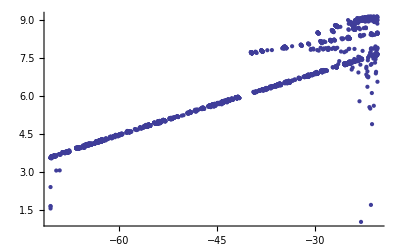

```mathematica
ListPlot[plotlist,PlotRange->{{-15,-60},{0,14}}]
```